```mathematica
dataPath=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data/dataOccupancyPreprocessed.csv"}];
```

```mathematica
data=SemanticImport[dataPath,{"DateTime","Real","Real","Real","Real","Real","Boolean"},"Dataset",HeaderLines->1];
```

```mathematica
trainData=Values@Normal[data[[All,{"Temperature","Humidity","Light","CO2","HumidityRatio"}]]];
```

```mathematica
cluster[method_:"GaussianMixture",criterionFunction_:Automatic]:=Module[{clusters,rules,classifier},
clusters=ClusteringComponents[trainData,2,1,Method->method,PerformanceGoal->"Quality"];
rules=Map[clusters[[#]]->data[[#,"Occupancy"]]&,Range[Length[data]]];
classifier=Classify[rules,Method->Automatic];
Return[ClassifierMeasurements[classifier,rules]];
]
```

```mathematica
cm=cluster["KMeans"];
```

```mathematica
cm["ClassMeanCrossEntropy"]
```

<|False→0.139434,True→0.567991|>

```mathematica
cm["Accuracy"]
```

0.900286

```mathematica
cm["FScore"]
```

<|False→0.934353,True→0.792723|>

```mathematica
cm["ClassMeanCrossEntropy"]
```

<|False→0.139434,True→0.567991|>

```mathematica
cm["Specificity"]
```

<|False→0.955355,True→0.886555|>

```mathematica
cm["Perplexity"]
```

1.25228

```mathematica
cm["Precision"]
```

<|False→0.987599,True→0.677407|>

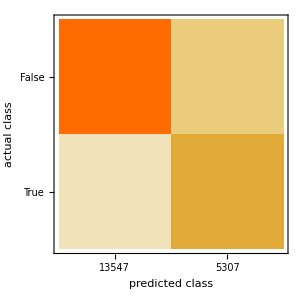

```mathematica
cm["ConfusionMatrixPlot"]
```

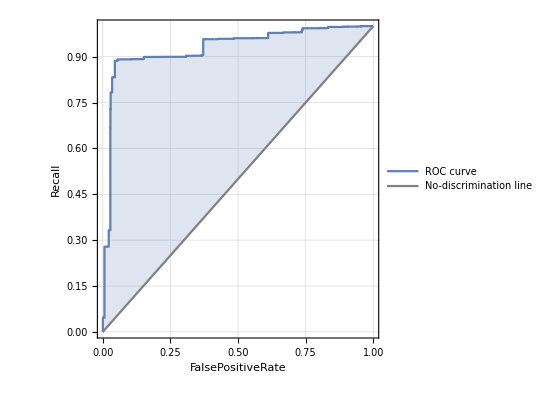
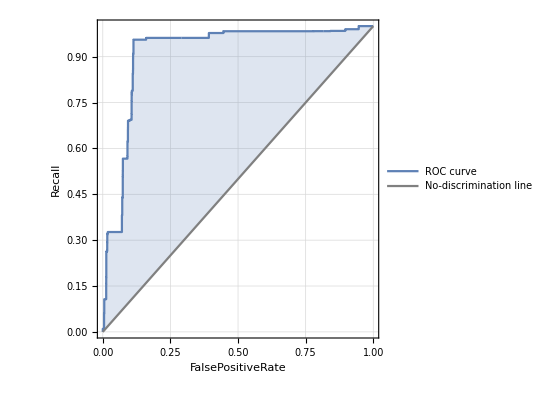
<|False→-Graphics-,True→-Graphics-|>

```mathematica
cm["ROCCurve"]
```